```mathematica
NSolve[50<x<100&&0.3835983465398391 ⅇ^(-0.46227810650887563 (-73.04+x)^2)==100 0.6649038006690545 ⅇ^(-1.388888888888889 (-67.27+x)^2),x]
NSolve[50<x<100&&0.3835983465398391 ⅇ^(-0.46227810650887563 (-73.04+x)^2)==.01 0.6649038006690545 ⅇ^(-1.388888888888889 (-67.27+x)^2),x]
```

{{x→58.8724},{x→69.9104}}

{{x→59.8615},{x→68.9213}}

```mathematica
NSolve[50<x<100&&0.3835983465398391 ⅇ^(-0.46227810650887563 (-73.04+x)^2)==0.6649038006690545 ⅇ^(-1.388888888888889 (-67.27+x)^2),x]
```

{{x→59.3427},{x→69.4401}}

```mathematica
Table[{x,m,s,(x-m)/s},{x,{59.342683522521895,69.44011026905238}},
{m,{67.27,73.04}},{s,{0.60,1.04}}]
```

{{{{59.3427,67.27,0.6,-13.2122},{59.3427,67.27,1.04,-7.62242}},{{59.3427,73.04,0.6,-22.8289},{59.3427,73.04,1.04,-13.1705}}},{{{69.4401,67.27,0.6,3.61685},{69.4401,67.27,1.04,2.08664}},{{69.4401,73.04,0.6,-5.99982},{69.4401,73.04,1.04,-3.46143}}}}

```mathematica
?N
```

```mathematica
PDF[NormalDistribution[73.04,1.04]][x] == 
PDF[NormalDistribution[67.27,0.60]][x]
```

0.383598 ⅇ^(-0.462278 (-73.04+x)^2)==0.664904 ⅇ^(-1.38889 (-67.27+x)^2)

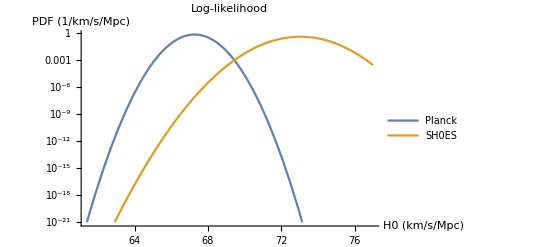

```mathematica
LogPlot[{
PDF[NormalDistribution[67.27,0.60]][x],
PDF[NormalDistribution[73.04,1.04]][x]
},{x,57,77},
PlotRange->{All,{10^-21,All}},
PlotLabel->"Log-likelihood",
AxesLabel->{"H0 (km/s/Mpc)", "PDF (1/km/s/Mpc)"},
PlotLegends->{"Planck", "SH0ES"}]
```

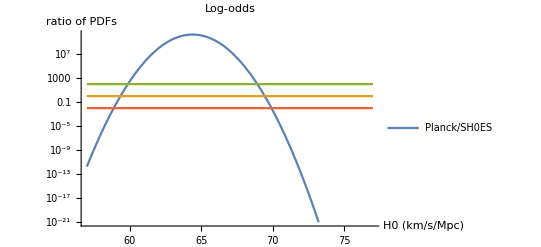

```mathematica
LogPlot[{
PDF[NormalDistribution[67.27,0.60]][x]/
PDF[NormalDistribution[73.04,1.04]][x],1,100,.01
},{x,57,77},
PlotRange->{All,{10^-21,All}},
PlotLabel->"Log-odds",
AxesLabel->{"H0 (km/s/Mpc)", "ratio of PDFs"},
PlotLegends->{"Planck/SH0ES"}]
```